## Алгоритмы восстановления пробелов в тексте

Задача сегментации текста возникает в различных прикладных задах, например, в задаче исправления опечаток в тексте пользователя, при анализе хештэгов в социальных сетях и т.д.

В качестве примера рассмотрим строку:

```mathematica
Text[Style["tableapplecharitablecupboarding",20]]
```

tableapplecharitablecupboarding

Можно заметить, что расставить пробелы в данном тексте можно четырьмя различными способами:

```mathematica
Module[{string,positions},string="tableapplecharitablecupboarding";
positions=StringPosition[string,Alternatives@@DictionaryLookup[],Overlaps->All];
Style[StringTake[string,Pick[positions,#]],20]&/@SatisfiabilityInstances[And@@(BooleanCountingFunction[{1},Length@positions]@@@Transpose@MapIndexed[Function[{list,index},#&&c@@index&/@list],Table[#1≤i≤#2,{i,StringLength@string}]&@@@positions]),Array[c,Length@positions],All]]//TableForm
```

{table,apple,char,it,able,cup,boar,ding}
{table,apple,char,it,able,cup,boarding}
{table,apple,charitable,cup,boar,ding}
{table,apple,charitable,cup,boarding}

Таким образом, необходимо разработать алгоритмы, которые позволят восстановить пробелы в тексте.

## 1. Алгоритмы на основе корпуса слов

Под корпусом слов подразумевается заранее определенный словарь известных слов, которые могут встретиться в тексте. В приведенном выше примере текст был разделен на основе встроенного в Wolfram Mathematica словаря (DictionaryLookup).

Суть представленных ниже алгоритмов состоит в том, чтобы, проходя последовательно по тексту, найти наилучшую последовательность слов внутри строки.

### 1.1. Алгоритм максимального соответствия

Алгоритм максимального соответствия – это жадный алгоритм, в котором в тексте последовательно выделяются слова наибольшей длины, которые встретились в словаре. В качестве примера приведем строку:

```mathematica
Row[{Text[Style["themendinehere  →  ",20]],Text[Style["the men dine here",Darker@Green,20]]}]
```

themendinehere  →  the men dine here

Данную строку также можно разбить несколькими способами. На графе ниже приведены все возможные варианты разбиения:

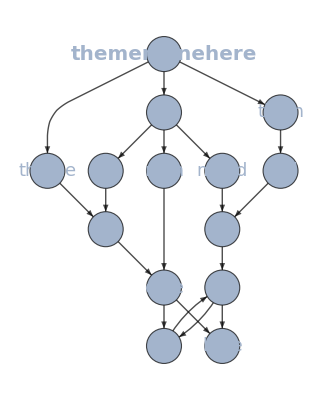

```mathematica
Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black]
```

На первом шаге алгоритма максимального соответствия будет выбрана подпоследовательность «theme», поскольку это наиболее длинное известное слово. Останется подпоследовательность «ndinehere», которую невозможно разделить, поскольку слов на «nd» не оказалось в словаре. В данном случае выбирается «n», а на следующем шаге рассматривается «dinehere».

```mathematica
pic1=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black];
pic2=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"theme","themendinehere"->"theme"},GraphHighlightStyle->"Thick"
];
pic3=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[Bold,20],"n"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"theme","themendinehere"->"theme","theme"->"n"},GraphHighlightStyle->"Thick"
];
pic4=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[Bold,20],"dine"->Directive[Bold,20],"n"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"theme","themendinehere"->"theme","theme"->"n","n"->"dine"},GraphHighlightStyle->"Thick"
];
pic5=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[Bold,20],"dine"->Directive[Bold,20],"n"->Directive[Bold,20],"here"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"theme","themendinehere"->"theme","theme"->"n","n"->"dine","dine"->"here"},GraphHighlightStyle->"Thick"
];
maximalMatchingExample={pic1,pic2,pic3,pic4,pic5};
Manipulate[maximalMatchingExample⟦k⟧,{{k,1,"step"},1,5,1},Paneled->False,ControlPlacement->Center]
```

Как видно из данного примера, алгоритм неверно выделил первое слово, что привело к неверному результату. Чтобы исправить данную ошибку, можно рассматривать обратный алгоритм.

### 1.2. Обратный алгоритм максимального соответствия

В отличие от предыдущего алгоритма поиск оптимального разбиения начинается с конца строки. Таким образом, подпоследовательностью наибольшей длины окажется слово «here».

```mathematica
pic6=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"here"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black
];
pic7=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"dine"->Directive[Bold,20],"here"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"dine"->"here"},GraphHighlightStyle->"Thick"
];
pic8=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"dine"->Directive[Bold,20],"men"->Directive[Bold,20],"here"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"dine"->"here","men"->"dine"},GraphHighlightStyle->"Thick"
];
pic9=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"dine"->Directive[Bold,20],"men"->Directive[Bold,20],"the"->Directive[Bold,20],"here"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"dine"->"here","men"->"dine","the"->"men","themendinehere"->"the"},GraphHighlightStyle->"Thick"
];
inverseMaximalMatchingExample={pic6,pic7,pic8,pic9};
Manipulate[inverseMaximalMatchingExample⟦k⟧,{{k,1,"step"},1,4,1},Paneled->False,ControlPlacement->Center]
```

### 1.3. Двунаправленный алгоритм максимального соответствия

Двунаправленный алгоритм является комбинацией предыдущих алгоритмов. На первом шаге данного алгоритма выполняются прямой поиск, т.е. применяется алгоритм максимального соответствия и обратный поиск. Затем рассматриваются все полученные слова и выбирается наименее сегментированная последовательность (с наименьшим количеством неизвестных слов).

### 1.4. Выделение подпоследовательности с наименьшим количеством слов

Указанный алгоритм рассматривает все возможные подпоследовательности и выбирает ту, где содержится наименьшее количество слов не из словаря. Ниже приведен пример реализации, где на каждом шаге из рассмотрения удаляются те ребра, по которым невозможна дальнейшая сегментация.

```mathematica
pic10=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black];
pic11=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->Black,
GraphHighlight->{"theme","themendinehere"->"theme","themendinehere"->"the","themendinehere"->"them"},GraphHighlightStyle->"Thick"
];
pic12=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[LightGray,18],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->{"themendinehere"->"theme"->LightGray,"theme"->"n"->LightGray,Black},
GraphHighlight->{"theme","themendinehere"->"the","themendinehere"->"them","them"->"end","the"->"me","the"->"men","the"->"mend"},GraphHighlightStyle->"Thick"
];
pic13=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[LightGray,18],"me"->Directive[LightGray,18],"n"->Directive[LightGray,18],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->{"themendinehere"->"theme"->LightGray,"theme"->"n"->LightGray,"the"->"me"->LightGray,"me"->"n"->LightGray,"n"->"dine"->LightGray,Black},
GraphHighlight->{"theme","themendinehere"->"the","themendinehere"->"them","them"->"end","the"->"men","the"->"mend","men"->"dine","mend"->"in","end"->"in"},GraphHighlightStyle->"Thick"
];
pic14=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[LightGray,18],"me"->Directive[LightGray,18],"n"->Directive[LightGray,18],"mend"->Directive[LightGray,18],"them"->Directive[LightGray,18],"end"->Directive[LightGray,18],"in"->Directive[LightGray,18],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->{
"themendinehere"->"theme"->LightGray,
"theme"->"n"->LightGray,
"the"->"me"->LightGray,
"me"->"n"->LightGray,
"n"->"dine"->LightGray,
"them"->"end"->LightGray,
"the"->"mend"->LightGray,
"end"->"in"->LightGray,
"mend"->"in"->LightGray,
"in"->"e"->LightGray,
"e"->"her"->LightGray,
"e"->"here"->LightGray,
Black},
GraphHighlight->{"theme","themendinehere"->"the","themendinehere"->"them","the"->"men","men"->"dine"},GraphHighlightStyle->"Thick"
];
pic15=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[LightGray,18],"me"->Directive[LightGray,18],"n"->Directive[LightGray,18],"mend"->Directive[LightGray,18],"them"->Directive[LightGray,18],"end"->Directive[LightGray,18],"in"->Directive[LightGray,18],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->{
"themendinehere"->"theme"->LightGray,
"theme"->"n"->LightGray,
"the"->"me"->LightGray,
"me"->"n"->LightGray,
"n"->"dine"->LightGray,
"them"->"end"->LightGray,
"the"->"mend"->LightGray,
"end"->"in"->LightGray,
"mend"->"in"->LightGray,
"in"->"e"->LightGray,
"e"->"her"->LightGray,
"e"->"here"->LightGray,
Black},
GraphHighlight->{"theme","themendinehere"->"the","themendinehere"->"them","the"->"men","men"->"dine","dine"->"here","dine"->"her"},GraphHighlightStyle->"Thick"
];
pic16=Graph[{"themendinehere"->"the","themendinehere"->"them","themendinehere"->"theme",
"the"->"me","the"->"men","the"->"mend","them"->"end","theme"->"n",
"me"->"n","men"->"dine","mend"->"in","end"->"in","n"->"dine",
"dine"->"her","dine"->"here","in"->"e",
"her"->"e","e"->"her","e"->"here"
},
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Placed["Name",Center],VertexLabelStyle->{"themendinehere"->Directive[Bold,20],"theme"->Directive[LightGray,18],"me"->Directive[LightGray,18],"n"->Directive[LightGray,18],"mend"->Directive[LightGray,18],"them"->Directive[LightGray,18],"end"->Directive[LightGray,18],"in"->Directive[LightGray,18],"her"->Directive[LightGray,18],"e"->Directive[LightGray,18],18},VertexShapeFunction->None,VertexSize->0.6,EdgeStyle->{
"themendinehere"->"theme"->LightGray,
"theme"->"n"->LightGray,
"the"->"me"->LightGray,
"me"->"n"->LightGray,
"n"->"dine"->LightGray,
"them"->"end"->LightGray,
"the"->"mend"->LightGray,
"end"->"in"->LightGray,
"mend"->"in"->LightGray,
"in"->"e"->LightGray,
"e"->"her"->LightGray,
"e"->"here"->LightGray,
"her"->"e"->LightGray,
"dine"->"her"->LightGray,
Black},
GraphHighlight->{"theme","themendinehere"->"the","themendinehere"->"them","the"->"men","men"->"dine","dine"->"here"},GraphHighlightStyle->"Thick"
];
maximumMatchingExample={pic10,pic11,pic12,pic13,pic14,pic15,pic16};
Manipulate[maximumMatchingExample⟦k⟧,{{k,1,"step"},1,7,1},Paneled->False,ControlPlacement->Center]
```